```mathematica
CacheRule2Problem[n_,m_]:=CacheRule2Problem[n,m]=With[
{P=Chromial[n], Q=Chromial[m]},
Problem[Take[CoefficientList[Q,x],-5],Take[CoefficientList[P,x],-5]]
]
```

```mathematica
Rule2Problem[n_,m_]:=With[
{P=Chromial[n], Q=Chromial[m]},
Problem[Prepend[CoefficientList[Q,x],0],CoefficientList[P,x]]
]
```

```mathematica
Clear[CacheRule2Problem]
```

```mathematica
Table[
With[{record = deps2[[k]]},
CacheRule2Problem[record[[1]],record[[2]]]

]
,{k,1,5}
]
```

{{18 x1m1-39 x2m1+29 x3m1-9 x4m1+x5m1,18 x1m2-39 x2m2+29 x3m2-9 x4m2+x5m2,18 x1m3-39 x2m3+29 x3m3-9 x4m3+x5m3,18 x1m4-39 x2m4+29 x3m4-9 x4m4+x5m4,18 x1m5-39 x2m5+29 x3m5-9 x4m5+x5m5}=={0,-6,11,-6,1},{135 x1m1-126 x2m1+56 x3m1-12 x4m1+x5m1,135 x1m2-126 x2m2+56 x3m2-12 x4m2+x5m2,135 x1m3-126 x2m3+56 x3m3-12 x4m3+x5m3,135 x1m4-126 x2m4+56 x3m4-12 x4m4+x5m4,135 x1m5-126 x2m5+56 x3m5-12 x4m5+x5m5}=={18,-39,29,-9,1},{154 x1m1-137 x2m1+58 x3m1-12 x4m1+x5m1,154 x1m2-137 x2m2+58 x3m2-12 x4m2+x5m2,154 x1m3-137 x2m3+58 x3m3-12 x4m3+x5m3,154 x1m4-137 x2m4+58 x3m4-12 x4m4+x5m4,154 x1m5-137 x2m5+58 x3m5-12 x4m5+x5m5}=={18,-39,29,-9,1},{513 x1m1-294 x2m1+92 x3m1-15 x4m1+x5m1,513 x1m2-294 x2m2+92 x3m2-15 x4m2+x5m2,513 x1m3-294 x2m3+92 x3m3-15 x4m3+x5m3,513 x1m4-294 x2m4+92 x3m4-15 x4m4+x5m4,513 x1m5-294 x2m5+92 x3m5-15 x4m5+x5m5}=={135,-126,56,-12,1},{565 x1m1-311 x2m1+94 x3m1-15 x4m1+x5m1,565 x1m2-311 x2m2+94 x3m2-15 x4m2+x5m2,565 x1m3-311 x2m3+94 x3m3-15 x4m3+x5m3,565 x1m4-311 x2m4+94 x3m4-15 x4m4+x5m4,565 x1m5-311 x2m5+94 x3m5-15 x4m5+x5m5}=={135,-126,56,-12,1}}

```mathematica
Rule2Problem[8,16]
```

{162 x3m1-459 x4m1+513 x5m1-294 x6m1+92 x7m1-15 x8m1+x9m1,162 x3m2-459 x4m2+513 x5m2-294 x6m2+92 x7m2-15 x8m2+x9m2,162 x3m3-459 x4m3+513 x5m3-294 x6m3+92 x7m3-15 x8m3+x9m3,162 x3m4-459 x4m4+513 x5m4-294 x6m4+92 x7m4-15 x8m4+x9m4,162 x3m5-459 x4m5+513 x5m5-294 x6m5+92 x7m5-15 x8m5+x9m5,162 x3m6-459 x4m6+513 x5m6-294 x6m6+92 x7m6-15 x8m6+x9m6,162 x3m7-459 x4m7+513 x5m7-294 x6m7+92 x7m7-15 x8m7+x9m7,162 x3m8-459 x4m8+513 x5m8-294 x6m8+92 x7m8-15 x8m8+x9m8,162 x3m9-459 x4m9+513 x5m9-294 x6m9+92 x7m9-15 x8m9+x9m9}=={0,-486,1539,-1998,1395,-570,137,-18,1}

```mathematica
Chrom[1]
```

24

```mathematica
CoefficientList[Chromial[2],x]
```

{0,18,-39,29,-9,1}

```mathematica
Table[
With[{record = deps2[[k]]},
record[[2]]

]
,{k,1,5}
]
```

{2,3,4,5,6}

```mathematica
Monitor[
Table[
With[{record = deps2[[k]]},
{Factor[PolynomialGCD[Chromial[ record[[1]]],Chromial[record[[2]]]]],record[[4]]}

]
,{k,1,100}
]//DeleteDuplicates,
k]
```

Part::partw: Part 4 of {1, 2, "{2,1<->4,2<->3}"} does not exist.

Part::partw: Part 4 of {2, 3, "{2,2<->4,3<->5}"} does not exist.

Part::partw: Part 4 of {2, 4, "{2,2<->5,1<->4}"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{(-3+x) (-2+x) (-1+x) x,{1,2,{2,1<->4,2<->3}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{2,3,{2,2<->4,3<->5}}⟦4⟧},{(-2+x) (-1+x) x,{2,4,{2,2<->5,1<->4}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{3,5,{2,1<->5,2<->3}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{3,6,{2,2<->5,1<->6}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{3,7,{2,3<->5,1<->4}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{3,8,{2,2<->6,3<->5}}⟦4⟧},{(-2+x) (-1+x) x,{4,7,{2,2<->4,3<->6}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{5,10,{2,3<->4,5<->6}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{5,11,{2,3<->5,4<->7}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{5,12,{2,4<->5,3<->6}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{5,13,{2,2<->6,3<->5}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{5,14,{2,3<->6,2<->4}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{5,15,{2,2<->5,6<->7}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{6,11,{2,1<->5,3<->7}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{6,18,{2,3<->5,1<->4}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{6,14,{2,3<->4,5<->6}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{7,18,{2,1<->5,2<->7}}⟦4⟧},{(-2+x) (-1+x) x,{7,21,{2,2<->6,3<->5}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{8,13,{2,1<->5,2<->3}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{8,14,{2,2<->5,1<->7}}⟦4⟧},{(-2+x) (-1+x) x,{8,21,{2,3<->5,1<->4}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{8,22,{2,4<->6,3<->5}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{8,20,{2,3<->7,2<->6}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{9,16,{2,1<->5,2<->3}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{9,20,{2,2<->5,1<->6}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{9,11,{2,3<->5,1<->4}}⟦4⟧},{(-3+x)^4 (-2+x) (-1+x) x,{9,17,{2,3<->4,5<->6}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{10,24,{2,2<->6,3<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{10,25,{2,3<->6,2<->8}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{10,26,{2,5<->6,2<->4}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{10,27,{2,4<->5,6<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{10,28,{2,4<->6,5<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{10,29,{2,1<->7,2<->3}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{10,30,{2,2<->7,1<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{10,31,{2,3<->5,7<->8}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{11,37,{2,2<->6,3<->5}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{11,38,{2,3<->6,2<->4}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{11,36,{2,3<->4,6<->8}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),{11,39,{2,1<->7,2<->3}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{11,40,{2,2<->7,1<->5}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{11,41,{2,3<->7,1<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{12,47,{2,2<->6,3<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{12,39,{2,3<->6,2<->4}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{12,28,{2,3<->4,6<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{12,48,{2,4<->6,3<->8}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{12,49,{2,2<->5,6<->7}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{12,50,{2,1<->7,2<->3}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{12,30,{2,2<->7,1<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{12,43,{2,3<->5,7<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{13,24,{2,3<->4,5<->6}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{13,37,{2,3<->5,4<->7}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{13,47,{2,4<->5,3<->6}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{13,30,{2,3<->6,4<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{13,54,{2,4<->6,3<->5}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{13,55,{2,1<->7,2<->3}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{13,56,{2,2<->7,1<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{13,49,{2,2<->5,7<->8}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{13,57,{2,3<->8,2<->6}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{14,26,{2,3<->4,5<->8}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{14,38,{2,3<->5,4<->7}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{14,39,{2,4<->5,3<->6}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{14,56,{2,1<->7,2<->3}}⟦4⟧},{(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{14,62,{2,2<->7,1<->5}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{15,25,{2,3<->4,5<->6}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{15,38,{2,3<->5,4<->7}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{15,49,{2,4<->5,3<->6}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{15,43,{2,2<->6,3<->8}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{15,36,{2,5<->6,4<->8}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{15,44,{2,2<->8,6<->7}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{16,32,{2,3<->4,5<->6}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{16,42,{2,3<->5,4<->7}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{16,51,{2,4<->5,3<->6}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{16,39,{2,3<->6,4<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{16,60,{2,4<->6,3<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{16,65,{2,2<->5,6<->7}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{16,57,{2,2<->6,5<->8}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{16,64,{2,5<->6,2<->4}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{16,59,{2,1<->7,2<->3}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{16,63,{2,2<->7,1<->5}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{16,61,{2,3<->8,2<->6}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{16,68,{2,6<->8,2<->3}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{17,32,{2,3<->4,5<->6}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{17,44,{2,3<->5,4<->7}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{17,52,{2,4<->5,3<->6}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{17,57,{2,2<->6,3<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{17,61,{2,4<->6,3<->5}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{17,26,{2,5<->6,4<->8}}⟦4⟧},{(-3+x)^5 (-2+x) (-1+x) x,{17,58,{2,1<->7,2<->3}}⟦4⟧},{(-3+x)^3 (-2+x) (-1+x) x,{17,63,{2,2<->7,1<->5}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{18,40,{2,2<->6,3<->5}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{18,41,{2,3<->6,2<->4}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{18,46,{2,2<->5,6<->7}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{19,31,{2,2<->6,3<->5}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{19,36,{2,5<->6,2<->4}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{19,35,{2,4<->5,6<->8}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),{20,57,{2,3<->4,5<->6}}⟦4⟧},{(-3+x) (-2+x) (-1+x) x,{20,40,{2,3<->5,4<->8}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{20,42,{2,2<->6,3<->7}}⟦4⟧},{(-3+x)^2 (-2+x) (-1+x) x,{20,38,{2,3<->6,2<->4}}⟦4⟧}}

```mathematica
matie=With[{size=5},
Flatten[
Matt[size]/.Solve[
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
With[{record = deps2[[k]]},
CacheRule2Problem[record[[1]],record[[2]]]

]
,{k,3,10}
],
k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]

];MatrixForm[matie]
```

7

(x1m1
x1m2
x1m3
x1m4
x1m5
x2m1
x2m2
x2m3
x2m4
x2m5
x3m1
x3m2
x3m3
x3m4
x3m5
x4m1
x4m2
x4m3
x4m4
x4m5
x5m1
x5m2
x5m3
x5m4
x5m5)

```mathematica
Select[chroms,Exponent[#,x]==6&]
```

{-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6}

```mathematica
PolynomialGCD[-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6,-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6]
```

2 x-3 x^2+x^3

```mathematica
Select[chroms,Exponent[#,x]==7&]
```

{162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,192 x-526 x^2+565 x^3-311 x^4+94 x^5-15 x^6+x^7,210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7}

```mathematica
PolynomialGCD[162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7,192 x-526 x^2+565 x^3-311 x^4+94 x^5-15 x^6+x^7,210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7]
```

```mathematica
Factor[-6 x+11 x^2-6 x^3+x^4]
```

(-3+x) (-2+x) (-1+x) x

```mathematica
Select[chroms,Exponent[#,x]==8&]
```

{-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-630 x+1905 x^2-2347 x^3+1554 x^4-605 x^5+140 x^6-18 x^7+x^8,-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,-714 x+2107 x^2-2525 x^3+1627 x^4-619 x^5+141 x^6-18 x^7+x^8,-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8}

```mathematica
PolynomialGCD[-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8,-630 x+1905 x^2-2347 x^3+1554 x^4-605 x^5+140 x^6-18 x^7+x^8,-576 x+1770 x^2-2221 x^3+1498 x^4-593 x^5+139 x^6-18 x^7+x^8,-714 x+2107 x^2-2525 x^3+1627 x^4-619 x^5+141 x^6-18 x^7+x^8,-664 x+1992 x^2-2432 x^3+1595 x^4-615 x^5+141 x^6-18 x^7+x^8]
```

2 x-3 x^2+x^3

```mathematica
Factor[2 x-3 x^2+x^3]
```

(-2+x) (-1+x) x

```mathematica
Select[chroms,Exponent[#,x]==9&]
```

{1458 x-5103 x^2+7533 x^3-6183 x^4+3105 x^5-981 x^6+191 x^7-21 x^8+x^9,1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9,1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9,2142 x-7035 x^2+9682 x^3-7406 x^4+3484 x^5-1042 x^6+195 x^7-21 x^8+x^9,1992 x-6640 x^2+9288 x^3-7217 x^4+3440 x^5-1038 x^6+195 x^7-21 x^8+x^9,2298 x-7465 x^2+10150 x^3-7670 x^4+3567 x^5-1056 x^6+196 x^7-21 x^8+x^9,2388 x-7696 x^2+10373 x^3-7773 x^4+3590 x^5-1058 x^6+196 x^7-21 x^8+x^9,2532 x-8062 x^2+10722 x^3-7932 x^4+3625 x^5-1061 x^6+196 x^7-21 x^8+x^9,2048 x-6784 x^2+9426 x^3-7279 x^4+3453 x^5-1039 x^6+195 x^7-21 x^8+x^9,2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9}

```mathematica
PolynomialLCM[1458 x-5103 x^2+7533 x^3-6183 x^4+3105 x^5-981 x^6+191 x^7-21 x^8+x^9,1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9,1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9,2142 x-7035 x^2+9682 x^3-7406 x^4+3484 x^5-1042 x^6+195 x^7-21 x^8+x^9,1992 x-6640 x^2+9288 x^3-7217 x^4+3440 x^5-1038 x^6+195 x^7-21 x^8+x^9,2298 x-7465 x^2+10150 x^3-7670 x^4+3567 x^5-1056 x^6+196 x^7-21 x^8+x^9,2388 x-7696 x^2+10373 x^3-7773 x^4+3590 x^5-1058 x^6+196 x^7-21 x^8+x^9,2532 x-8062 x^2+10722 x^3-7932 x^4+3625 x^5-1061 x^6+196 x^7-21 x^8+x^9,2048 x-6784 x^2+9426 x^3-7279 x^4+3453 x^5-1039 x^6+195 x^7-21 x^8+x^9,2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9]
```

(-3+x)^6 (-32+29 x-9 x^2+x^3)^2 (-35+30 x-9 x^2+x^3) (2 x-3 x^2+x^3) (119-133 x+58 x^2-12 x^3+x^4) (-332+498 x-303 x^2+94 x^3-15 x^4+x^5) (-422+570 x-320 x^2+95 x^3-15 x^4+x^5) (-398+553 x-317 x^2+95 x^3-15 x^4+x^5) (-383+542 x-315 x^2+95 x^3-15 x^4+x^5) (-343+511 x-309 x^2+95 x^3-15 x^4+x^5)

```mathematica
PolynomialGCD[1458 x-5103 x^2+7533 x^3-6183 x^4+3105 x^5-981 x^6+191 x^7-21 x^8+x^9,1728 x-5886 x^2+8433 x^3-6715 x^4+3277 x^5-1010 x^6+193 x^7-21 x^8+x^9,1890 x-6345 x^2+8946 x^3-7009 x^4+3369 x^5-1025 x^6+194 x^7-21 x^8+x^9,2142 x-7035 x^2+9682 x^3-7406 x^4+3484 x^5-1042 x^6+195 x^7-21 x^8+x^9,1992 x-6640 x^2+9288 x^3-7217 x^4+3440 x^5-1038 x^6+195 x^7-21 x^8+x^9,2298 x-7465 x^2+10150 x^3-7670 x^4+3567 x^5-1056 x^6+196 x^7-21 x^8+x^9,2388 x-7696 x^2+10373 x^3-7773 x^4+3590 x^5-1058 x^6+196 x^7-21 x^8+x^9,2532 x-8062 x^2+10722 x^3-7932 x^4+3625 x^5-1061 x^6+196 x^7-21 x^8+x^9,2048 x-6784 x^2+9426 x^3-7279 x^4+3453 x^5-1039 x^6+195 x^7-21 x^8+x^9,2058 x-6839 x^2+9533 x^3-7378 x^4+3500 x^5-1050 x^6+196 x^7-21 x^8+x^9]
```

2 x-3 x^2+x^3

```mathematica
Select[chroms,Exponent[#,x]==10&]
```

{-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10,-5184 x+19386 x^2-31185 x^3+28578 x^4-16546 x^5+6307 x^6-1589 x^7+256 x^8-24 x^9+x^10,-5976 x+21912 x^2-34504 x^3+30939 x^4-17537 x^5+6554 x^6-1623 x^7+258 x^8-24 x^9+x^10,-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10,-6894 x+24693 x^2-37915 x^3+33160 x^4-18371 x^5+6735 x^6-1644 x^7+259 x^8-24 x^9+x^10,-6144 x+22400 x^2-35062 x^3+31263 x^4-17638 x^5+6570 x^6-1624 x^7+258 x^8-24 x^9+x^10,-7164 x+25476 x^2-38815 x^3+33692 x^4-18543 x^5+6764 x^6-1646 x^7+259 x^8-24 x^9+x^10,-7596 x+26718 x^2-40228 x^3+34518 x^4-18807 x^5+6808 x^6-1649 x^7+259 x^8-24 x^9+x^10,-6720 x+24170 x^2-37283 x^3+32761 x^4-18231 x^5+6709 x^6-1642 x^7+259 x^8-24 x^9+x^10,-8046 x+28071 x^2-41898 x^3+35643 x^4-19263 x^5+6921 x^6-1665 x^7+260 x^8-24 x^9+x^10,-7884 x+27612 x^2-41385 x^3+35349 x^4-19171 x^5+6906 x^6-1664 x^7+260 x^8-24 x^9+x^10,-8976 x+30664 x^2-44738 x^3+37233 x^4-19748 x^5+6998 x^6-1670 x^7+260 x^8-24 x^9+x^10,-6174 x+22575 x^2-35438 x^3+31667 x^4-17878 x^5+6650 x^6-1638 x^7+259 x^8-24 x^9+x^10,-7194 x+25651 x^2-39191 x^3+34096 x^4-18783 x^5+6844 x^6-1660 x^7+260 x^8-24 x^9+x^10,-7626 x+26893 x^2-40604 x^3+34922 x^4-19047 x^5+6888 x^6-1663 x^7+260 x^8-24 x^9+x^10,-8310 x+28825 x^2-42753 x^3+36145 x^4-19426 x^5+6949 x^6-1667 x^7+260 x^8-24 x^9+x^10,-8724 x+29974 x^2-44002 x^3+36836 x^4-19633 x^5+6981 x^6-1669 x^7+260 x^8-24 x^9+x^10,-7456 x+26390 x^2-40005 x^3+34547 x^4-18915 x^5+6863 x^6-1661 x^7+260 x^8-24 x^9+x^10,-6304 x+23030 x^2-36115 x^3+32228 x^4-18158 x^5+6734 x^6-1652 x^7+260 x^8-24 x^9+x^10}

```mathematica
PolynomialGCD[-4374 x+16767 x^2-27702 x^3+26082 x^4-15498 x^5+6048 x^6-1554 x^7+254 x^8-24 x^9+x^10,-5670 x+20925 x^2-33183 x^3+29973 x^4-17116 x^5+6444 x^6-1607 x^7+257 x^8-24 x^9+x^10,-5184 x+19386 x^2-31185 x^3+28578 x^4-16546 x^5+6307 x^6-1589 x^7+256 x^8-24 x^9+x^10,-5976 x+21912 x^2-34504 x^3+30939 x^4-17537 x^5+6554 x^6-1623 x^7+258 x^8-24 x^9+x^10,-6426 x+23247 x^2-36081 x^3+31900 x^4-17858 x^5+6610 x^6-1627 x^7+258 x^8-24 x^9+x^10,-6894 x+24693 x^2-37915 x^3+33160 x^4-18371 x^5+6735 x^6-1644 x^7+259 x^8-24 x^9+x^10,-6144 x+22400 x^2-35062 x^3+31263 x^4-17638 x^5+6570 x^6-1624 x^7+258 x^8-24 x^9+x^10,-7164 x+25476 x^2-38815 x^3+33692 x^4-18543 x^5+6764 x^6-1646 x^7+259 x^8-24 x^9+x^10,-7596 x+26718 x^2-40228 x^3+34518 x^4-18807 x^5+6808 x^6-1649 x^7+259 x^8-24 x^9+x^10,-6720 x+24170 x^2-37283 x^3+32761 x^4-18231 x^5+6709 x^6-1642 x^7+259 x^8-24 x^9+x^10,-8046 x+28071 x^2-41898 x^3+35643 x^4-19263 x^5+6921 x^6-1665 x^7+260 x^8-24 x^9+x^10,-7884 x+27612 x^2-41385 x^3+35349 x^4-19171 x^5+6906 x^6-1664 x^7+260 x^8-24 x^9+x^10,-8976 x+30664 x^2-44738 x^3+37233 x^4-19748 x^5+6998 x^6-1670 x^7+260 x^8-24 x^9+x^10,-6174 x+22575 x^2-35438 x^3+31667 x^4-17878 x^5+6650 x^6-1638 x^7+259 x^8-24 x^9+x^10,-7194 x+25651 x^2-39191 x^3+34096 x^4-18783 x^5+6844 x^6-1660 x^7+260 x^8-24 x^9+x^10,-7626 x+26893 x^2-40604 x^3+34922 x^4-19047 x^5+6888 x^6-1663 x^7+260 x^8-24 x^9+x^10,-8310 x+28825 x^2-42753 x^3+36145 x^4-19426 x^5+6949 x^6-1667 x^7+260 x^8-24 x^9+x^10,-8724 x+29974 x^2-44002 x^3+36836 x^4-19633 x^5+6981 x^6-1669 x^7+260 x^8-24 x^9+x^10,-7456 x+26390 x^2-40005 x^3+34547 x^4-18915 x^5+6863 x^6-1661 x^7+260 x^8-24 x^9+x^10,-6304 x+23030 x^2-36115 x^3+32228 x^4-18158 x^5+6734 x^6-1652 x^7+260 x^8-24 x^9+x^10]
```

2 x-3 x^2+x^3

```mathematica
GroebnerBasis[%190,{x}]
```

{2 x-3 x^2+x^3}

```mathematica
Select[chroms,Exponent[#,x]==11&]
```

{13122 x-54675 x^2+99873 x^3-105948 x^4+72576 x^5-33642 x^6+10710 x^7-2316 x^8+326 x^9-27 x^10+x^11,15552 x-63342 x^2+112941 x^3-116919 x^4+78216 x^5-35467 x^6+11074 x^7-2357 x^8+328 x^9-27 x^10+x^11,17928 x-71712 x^2+125424 x^3-127321 x^4+83550 x^5-37199 x^6+11423 x^7-2397 x^8+330 x^9-27 x^10+x^11,17010 x-68445 x^2+120474 x^3-123102 x^4+81321 x^5-36448 x^6+11265 x^7-2378 x^8+329 x^9-27 x^10+x^11,20682 x-80973 x^2+138438 x^3-137395 x^4+88273 x^5-38576 x^6+11667 x^7-2421 x^8+331 x^9-27 x^10+x^11,19278 x-76167 x^2+131490 x^3-131781 x^4+85474 x^5-37688 x^6+11491 x^7-2401 x^8+330 x^9-27 x^10+x^11,22878 x-88305 x^2+148705 x^3-145370 x^4+92063 x^5-39711 x^6+11877 x^7-2443 x^8+332 x^9-27 x^10+x^11,20160 x-79230 x^2+136019 x^3-135566 x^4+87454 x^5-38358 x^6+11635 x^7-2419 x^8+331 x^9-27 x^10+x^11,21492 x-83592 x^2+141921 x^3-139891 x^4+89321 x^5-38835 x^6+11702 x^7-2423 x^8+331 x^9-27 x^10+x^11,22050 x-85575 x^2+144965 x^3-142575 x^4+90823 x^5-39383 x^6+11829 x^7-2440 x^8+332 x^9-27 x^10+x^11,24138 x-92259 x^2+153765 x^3-148827 x^4+93432 x^5-40026 x^6+11916 x^7-2445 x^8+332 x^9-27 x^10+x^11,26262 x-99201 x^2+163283 x^3-156098 x^4+96859 x^5-41056 x^6+12110 x^7-2466 x^8+333 x^9-27 x^10+x^11,24930 x-94785 x^2+157084 x^3-151188 x^4+94423 x^5-40273 x^6+11950 x^7-2447 x^8+332 x^9-27 x^10+x^11,22788 x-87750 x^2+147402 x^3-143782 x^4+90939 x^5-39231 x^6+11755 x^7-2426 x^8+331 x^9-27 x^10+x^11,21582 x-84147 x^2+143224 x^3-141479 x^4+90445 x^5-39315 x^6+11824 x^7-2440 x^8+332 x^9-27 x^10+x^11,18432 x-73344 x^2+127586 x^3-128851 x^4+84177 x^5-37348 x^6+11442 x^7-2398 x^8+330 x^9-27 x^10+x^11,22848 x-88130 x^2+148329 x^3-144966 x^4+91823 x^5-39631 x^6+11863 x^7-2442 x^8+332 x^9-27 x^10+x^11,25020 x-95340 x^2+158387 x^3-152776 x^4+95547 x^5-40753 x^6+12072 x^7-2464 x^8+333 x^9-27 x^10+x^11,23652 x-90720 x^2+151767 x^3-147432 x^4+92862 x^5-39889 x^6+11898 x^7-2444 x^8+332 x^9-27 x^10+x^11,18522 x-73899 x^2+128889 x^3-130439 x^4+85301 x^5-37828 x^6+11564 x^7-2415 x^8+331 x^9-27 x^10+x^11,26172 x-98646 x^2+161980 x^3-154510 x^4+95735 x^5-40576 x^6+11988 x^7-2449 x^8+332 x^9-27 x^10+x^11,28242 x-105291 x^2+170913 x^3-161212 x^4+98856 x^5-41513 x^6+12167 x^7-2469 x^8+333 x^9-27 x^10+x^11,22368 x-86626 x^2+146405 x^3-143646 x^4+91292 x^5-39504 x^6+11846 x^7-2441 x^8+332 x^9-27 x^10+x^11,30198 x-111259 x^2+178334 x^3-166161 x^4+100787 x^5-41957 x^6+12223 x^7-2472 x^8+333 x^9-27 x^10+x^11,27018 x-101523 x^2+166181 x^3-158025 x^4+97601 x^5-41222 x^6+12130 x^7-2467 x^8+333 x^9-27 x^10+x^11,26928 x-100968 x^2+164878 x^3-156437 x^4+96477 x^5-40742 x^6+12008 x^7-2450 x^8+332 x^9-27 x^10+x^11,27498 x-103033 x^2+168134 x^3-159390 x^4+98162 x^5-41358 x^6+12148 x^7-2468 x^8+333 x^9-27 x^10+x^11,21248 x-83000 x^2+141568 x^3-140160 x^4+89815 x^5-39134 x^6+11795 x^7-2438 x^8+332 x^9-27 x^10+x^11,25788 x-97726 x^2+161404 x^3-154808 x^4+96337 x^5-40930 x^6+12093 x^7-2465 x^8+333 x^9-27 x^10+x^11,28992 x-107584 x^2+173766 x^3-163109 x^4+99589 x^5-41678 x^6+12187 x^7-2470 x^8+333 x^9-27 x^10+x^11,31368 x-114730 x^2+182481 x^3-168779 x^4+101736 x^5-42155 x^6+12245 x^7-2473 x^8+333 x^9-27 x^10+x^11,29460 x-109030 x^2+175600 x^3-164369 x^4+100102 x^5-41803 x^6+12204 x^7-2471 x^8+333 x^9-27 x^10+x^11,25482 x-96739 x^2+160083 x^3-153842 x^4+95916 x^5-40820 x^6+12077 x^7-2464 x^8+333 x^9-27 x^10+x^11,22170 x-86305 x^2+146644 x^3-144567 x^4+92187 x^5-39943 x^6+11965 x^7-2458 x^8+333 x^9-27 x^10+x^11,23772 x-91450 x^2+153446 x^3-149424 x^4+94226 x^5-40449 x^6+12034 x^7-2462 x^8+333 x^9-27 x^10+x^11,18912 x-75394 x^2+131375 x^3-132799 x^4+86702 x^5-38360 x^6+11690 x^7-2432 x^8+332 x^9-27 x^10+x^11,26292 x-99376 x^2+163659 x^3-156502 x^4+97099 x^5-41136 x^6+12124 x^7-2467 x^8+333 x^9-27 x^10+x^11,23442 x-90323 x^2+151823 x^3-148129 x^4+93604 x^5-40269 x^6+12005 x^7-2460 x^8+333 x^9-27 x^10+x^11,28272 x-105466 x^2+171289 x^3-161616 x^4+99096 x^5-41593 x^6+12181 x^7-2470 x^8+333 x^9-27 x^10+x^11,27048 x-101698 x^2+166557 x^3-158429 x^4+97841 x^5-41302 x^6+12144 x^7-2468 x^8+333 x^9-27 x^10+x^11,24258 x-92989 x^2+155444 x^3-150819 x^4+94796 x^5-40586 x^6+12052 x^7-2463 x^8+333 x^9-27 x^10+x^11,26720 x-100580 x^2+164946 x^3-157140 x^4+97220 x^5-41122 x^6+12115 x^7-2466 x^8+333 x^9-27 x^10+x^11,19170 x-76425 x^2+133172 x^3-134592 x^4+87822 x^5-38808 x^6+11802 x^7-2448 x^8+333 x^9-27 x^10+x^11}

```mathematica
PolynomialGCD[13122 x-54675 x^2+99873 x^3-105948 x^4+72576 x^5-33642 x^6+10710 x^7-2316 x^8+326 x^9-27 x^10+x^11,15552 x-63342 x^2+112941 x^3-116919 x^4+78216 x^5-35467 x^6+11074 x^7-2357 x^8+328 x^9-27 x^10+x^11,17928 x-71712 x^2+125424 x^3-127321 x^4+83550 x^5-37199 x^6+11423 x^7-2397 x^8+330 x^9-27 x^10+x^11,17010 x-68445 x^2+120474 x^3-123102 x^4+81321 x^5-36448 x^6+11265 x^7-2378 x^8+329 x^9-27 x^10+x^11,20682 x-80973 x^2+138438 x^3-137395 x^4+88273 x^5-38576 x^6+11667 x^7-2421 x^8+331 x^9-27 x^10+x^11,19278 x-76167 x^2+131490 x^3-131781 x^4+85474 x^5-37688 x^6+11491 x^7-2401 x^8+330 x^9-27 x^10+x^11,22878 x-88305 x^2+148705 x^3-145370 x^4+92063 x^5-39711 x^6+11877 x^7-2443 x^8+332 x^9-27 x^10+x^11,20160 x-79230 x^2+136019 x^3-135566 x^4+87454 x^5-38358 x^6+11635 x^7-2419 x^8+331 x^9-27 x^10+x^11,21492 x-83592 x^2+141921 x^3-139891 x^4+89321 x^5-38835 x^6+11702 x^7-2423 x^8+331 x^9-27 x^10+x^11,22050 x-85575 x^2+144965 x^3-142575 x^4+90823 x^5-39383 x^6+11829 x^7-2440 x^8+332 x^9-27 x^10+x^11,24138 x-92259 x^2+153765 x^3-148827 x^4+93432 x^5-40026 x^6+11916 x^7-2445 x^8+332 x^9-27 x^10+x^11,26262 x-99201 x^2+163283 x^3-156098 x^4+96859 x^5-41056 x^6+12110 x^7-2466 x^8+333 x^9-27 x^10+x^11,24930 x-94785 x^2+157084 x^3-151188 x^4+94423 x^5-40273 x^6+11950 x^7-2447 x^8+332 x^9-27 x^10+x^11,22788 x-87750 x^2+147402 x^3-143782 x^4+90939 x^5-39231 x^6+11755 x^7-2426 x^8+331 x^9-27 x^10+x^11,21582 x-84147 x^2+143224 x^3-141479 x^4+90445 x^5-39315 x^6+11824 x^7-2440 x^8+332 x^9-27 x^10+x^11,18432 x-73344 x^2+127586 x^3-128851 x^4+84177 x^5-37348 x^6+11442 x^7-2398 x^8+330 x^9-27 x^10+x^11,22848 x-88130 x^2+148329 x^3-144966 x^4+91823 x^5-39631 x^6+11863 x^7-2442 x^8+332 x^9-27 x^10+x^11,25020 x-95340 x^2+158387 x^3-152776 x^4+95547 x^5-40753 x^6+12072 x^7-2464 x^8+333 x^9-27 x^10+x^11,23652 x-90720 x^2+151767 x^3-147432 x^4+92862 x^5-39889 x^6+11898 x^7-2444 x^8+332 x^9-27 x^10+x^11,18522 x-73899 x^2+128889 x^3-130439 x^4+85301 x^5-37828 x^6+11564 x^7-2415 x^8+331 x^9-27 x^10+x^11,26172 x-98646 x^2+161980 x^3-154510 x^4+95735 x^5-40576 x^6+11988 x^7-2449 x^8+332 x^9-27 x^10+x^11,28242 x-105291 x^2+170913 x^3-161212 x^4+98856 x^5-41513 x^6+12167 x^7-2469 x^8+333 x^9-27 x^10+x^11,22368 x-86626 x^2+146405 x^3-143646 x^4+91292 x^5-39504 x^6+11846 x^7-2441 x^8+332 x^9-27 x^10+x^11,30198 x-111259 x^2+178334 x^3-166161 x^4+100787 x^5-41957 x^6+12223 x^7-2472 x^8+333 x^9-27 x^10+x^11,27018 x-101523 x^2+166181 x^3-158025 x^4+97601 x^5-41222 x^6+12130 x^7-2467 x^8+333 x^9-27 x^10+x^11,26928 x-100968 x^2+164878 x^3-156437 x^4+96477 x^5-40742 x^6+12008 x^7-2450 x^8+332 x^9-27 x^10+x^11,27498 x-103033 x^2+168134 x^3-159390 x^4+98162 x^5-41358 x^6+12148 x^7-2468 x^8+333 x^9-27 x^10+x^11,21248 x-83000 x^2+141568 x^3-140160 x^4+89815 x^5-39134 x^6+11795 x^7-2438 x^8+332 x^9-27 x^10+x^11,25788 x-97726 x^2+161404 x^3-154808 x^4+96337 x^5-40930 x^6+12093 x^7-2465 x^8+333 x^9-27 x^10+x^11,28992 x-107584 x^2+173766 x^3-163109 x^4+99589 x^5-41678 x^6+12187 x^7-2470 x^8+333 x^9-27 x^10+x^11,31368 x-114730 x^2+182481 x^3-168779 x^4+101736 x^5-42155 x^6+12245 x^7-2473 x^8+333 x^9-27 x^10+x^11,29460 x-109030 x^2+175600 x^3-164369 x^4+100102 x^5-41803 x^6+12204 x^7-2471 x^8+333 x^9-27 x^10+x^11,25482 x-96739 x^2+160083 x^3-153842 x^4+95916 x^5-40820 x^6+12077 x^7-2464 x^8+333 x^9-27 x^10+x^11,22170 x-86305 x^2+146644 x^3-144567 x^4+92187 x^5-39943 x^6+11965 x^7-2458 x^8+333 x^9-27 x^10+x^11,23772 x-91450 x^2+153446 x^3-149424 x^4+94226 x^5-40449 x^6+12034 x^7-2462 x^8+333 x^9-27 x^10+x^11,18912 x-75394 x^2+131375 x^3-132799 x^4+86702 x^5-38360 x^6+11690 x^7-2432 x^8+332 x^9-27 x^10+x^11,26292 x-99376 x^2+163659 x^3-156502 x^4+97099 x^5-41136 x^6+12124 x^7-2467 x^8+333 x^9-27 x^10+x^11,23442 x-90323 x^2+151823 x^3-148129 x^4+93604 x^5-40269 x^6+12005 x^7-2460 x^8+333 x^9-27 x^10+x^11,28272 x-105466 x^2+171289 x^3-161616 x^4+99096 x^5-41593 x^6+12181 x^7-2470 x^8+333 x^9-27 x^10+x^11,27048 x-101698 x^2+166557 x^3-158429 x^4+97841 x^5-41302 x^6+12144 x^7-2468 x^8+333 x^9-27 x^10+x^11,24258 x-92989 x^2+155444 x^3-150819 x^4+94796 x^5-40586 x^6+12052 x^7-2463 x^8+333 x^9-27 x^10+x^11,26720 x-100580 x^2+164946 x^3-157140 x^4+97220 x^5-41122 x^6+12115 x^7-2466 x^8+333 x^9-27 x^10+x^11,19170 x-76425 x^2+133172 x^3-134592 x^4+87822 x^5-38808 x^6+11802 x^7-2448 x^8+333 x^9-27 x^10+x^11]
```

2 x-3 x^2+x^3

```mathematica
Take[deps2,5]
```

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression]
```

{{1,2,{2,1<->4,2<->3}},{2,3,{2,2<->4,3<->5}},{2,4,{2,2<->5,1<->4}},{3,5,{2,1<->5,2<->3}},{3,6,{2,2<->5,1<->6}},{3,7,{2,3<->5,1<->4}},{3,8,{2,2<->6,3<->5}},{4,7,{2,2<->4,3<->6}},{5,10,{2,3<->4,5<->6}},{5,11,{2,3<->5,4<->7}},{5,12,{2,4<->5,3<->6}},1365031,{58714,373244,{2,5<->10,3<->7}},{58715,394789,{2,1<->5,2<->10}},{58715,398437,{2,4<->9,3<->5}},{58716,398406,{2,1<->5,2<->3}},{58716,398385,{2,2<->5,1<->13}},{58716,398437,{2,3<->5,1<->4}},{58716,398397,{2,3<->7,9<->10}},{58716,398391,{2,3<->9,7<->13}},{58716,398438,{2,7<->9,3<->5}},{58716,398402,{2,3<->10,6<->7}},{58716,398387,{2,3<->8,11<->12}}}
 |  |  |  |

```mathematica
Map[#[[2]]&,Map[{ PathBaseCoeff[Chromial[#[[1]]]]//Rest//Rest//Most//Most,PathBaseCoeff[Chromial[#[[2]]]]//Rest//Rest//Most//Most}&,deps2]]
```

{{-4,8},{8,-20,18},{11,-25,20},{-16,48,-56,32},{-22,61,-65,34},{-26,69,-70,35},{-16,48,-56,32},{-26,69,-70,35},{32,-112,160,-120,50},{52,-164,209,-140,53},{32,-112,160,-120,50},{32,-112,160,-120,50},{44,-144,191,-133,52},{44,-144,191,-133,52},{52,-164,209,-140,53},{66,-197,236,-149,54},{44,-144,191,-133,52},{66,-197,236,-149,54},{57,-176,220,-145,54},{32,-112,160,-120,50},{44,-144,191,-133,52},{57,-176,220,-145,54},{32,-112,160,-120,50},{44,-144,191,-133,52},{32,-112,160,-120,50},{44,-144,191,-133,52},{52,-164,209,-140,53},{32,-112,160,-120,50},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-64,256,-432,400,-220,72},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-114,409,-616,510,-253,76},{-132,460,-669,534,-257,76},{-132,460,-669,534,-257,76},{-104,380,-582,489,-246,75},{-150,509,-721,562,-265,77},{-162,541,-752,575,-267,77},{-64,256,-432,400,-220,72},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-114,409,-616,510,-253,76},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-64,256,-432,400,-220,72},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-88,332,-526,457,-237,74},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-132,460,-669,534,-257,76},{-104,380,-582,489,-246,75},{-88,332,-526,457,-237,74},{-121,429,-636,518,-254,76},{-88,332,-526,457,-237,74},{-132,460,-669,534,-257,76},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-132,460,-669,534,-257,76},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-88,332,-526,457,-237,74},{-88,332,-526,457,-237,74},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-64,256,-432,400,-220,72},{-64,256,-432,400,-220,72},{-64,256,-432,400,-220,72},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-64,256,-432,400,-220,72},{-104,380,-582,489,-246,75},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-150,509,-721,562,-265,77},{-162,541,-752,575,-267,77},{-182,593,-801,595,-270,77},{-104,380,-582,489,-246,75},{-132,460,-669,534,-257,76},{-88,332,-526,457,-237,74},{-88,332,-526,457,-237,74},{-150,509,-721,562,-265,77},{-104,380,-582,489,-246,75},{-132,460,-669,534,-257,76}}

```mathematica
def=DeleteDuplicates[Map[#[[2]]&,Monitor[Table[With[
{record=deps2[[k]]},
{ PathBaseCoeff[Chromial[record[[1]]]]//Rest//Rest//Most//Most,PathBaseCoeff[Chromial[record[[2]]]]//Rest//Rest//Most//Most}],{k,1,1200}],k]]]
```

{{-4,8},{8,-20,18},{11,-25,20},{-16,48,-56,32},{-22,61,-65,34},{-26,69,-70,35},{32,-112,160,-120,50},{52,-164,209,-140,53},{44,-144,191,-133,52},{66,-197,236,-149,54},{57,-176,220,-145,54},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-114,409,-616,510,-253,76},{-132,460,-669,534,-257,76},{-150,509,-721,562,-265,77},{-162,541,-752,575,-267,77},{-121,429,-636,518,-254,76},{-182,593,-801,595,-270,77},{-120,426,-637,525,-259,77},{128,-576,1120,-1232,840,-364,98},{208,-864,1544,-1560,981,-396,101},{176,-752,1384,-1440,931,-385,100},{228,-932,1641,-1636,1016,-405,102},{264,-1052,1798,-1737,1048,-409,102},{242,-979,1701,-1672,1026,-406,102},{286,-1123,1892,-1805,1078,-417,103},{324,-1244,2045,-1902,1109,-421,103},{300,-1168,1951,-1845,1092,-419,103},{364,-1368,2195,-1991,1135,-424,103},{388,-1440,2285,-2055,1164,-432,104},{404,-1488,2341,-2087,1173,-433,104},{240,-972,1700,-1687,1043,-413,103},{322,-1237,2044,-1917,1126,-428,104},{362,-1361,2194,-2006,1152,-431,104},{430,-1565,2431,-2140,1189,-435,104},{347,-1315,2137,-1969,1139,-429,104},{474,-1693,2574,-2217,1209,-437,104},{502,-1773,2661,-2262,1220,-438,104},{247,-995,1736,-1722,1064,-420,104},{-256,1280,-2816,3584,-2912,1568,-560,128},{-352,1680,-3520,4264,-3302,1701,-585,130},{-456,2092,-4214,4913,-3668,1826,-609,132},{-416,1936,-3952,4664,-3522,1773,-598,131},{-572,2532,-4907,5502,-3961,1912,-623,133},{-724,3084,-5749,6206,-4310,2014,-639,134},{-528,2368,-4648,5272,-3833,1866,-613,132},{-600,2636,-5070,5641,-4029,1930,-625,133},{-648,2812,-5334,5849,-4120,1951,-627,133},{-644,2796,-5325,5878,-4169,1982,-636,134},{-484,2200,-4381,5045,-3724,1838,-610,132},{-480,2184,-4372,5074,-3773,1869,-619,133},{-726,3091,-5750,6191,-4293,2007,-638,134},{-776,3268,-6010,6395,-4383,2028,-640,134},{-860,3560,-6427,6711,-4518,2059,-643,134},{-728,3100,-5758,6177,-4261,1983,-630,133},{-694,2977,-5589,6075,-4247,1997,-637,134},{-944,3844,-6832,7037,-4684,2114,-654,135},{-856,3544,-6418,6740,-4567,2090,-652,135},{-808,3380,-6170,6515,-4433,2039,-641,134},{-1034,4145,-7242,7330,-4800,2138,-656,135},{-948,3860,-6841,7008,-4635,2083,-645,134},{-1000,4032,-7086,7214,-4751,2127,-655,135},{-1092,4336,-7493,7499,-4862,2150,-657,135},{-1004,4048,-7095,7185,-4702,2096,-646,134},{-676,2912,-5489,5991,-4207,1987,-636,134},{-627,2734,-5226,5788,-4120,1967,-634,134}}

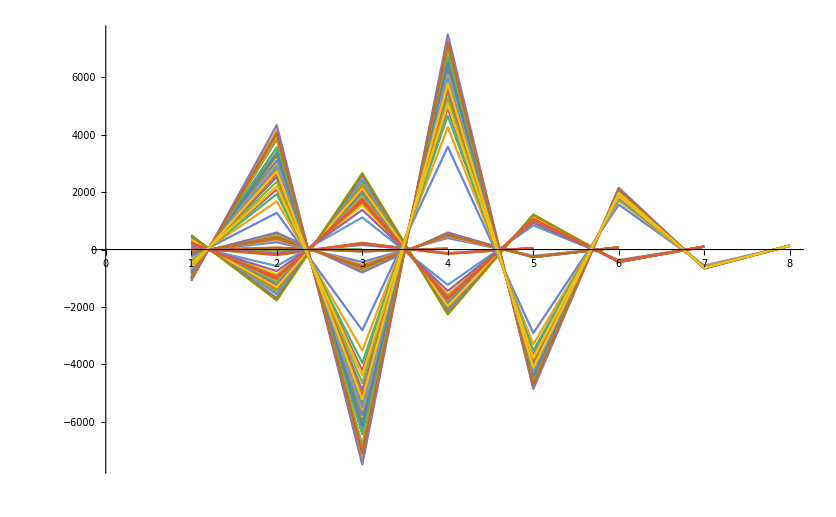

```mathematica
ListLinePlot[def]
```

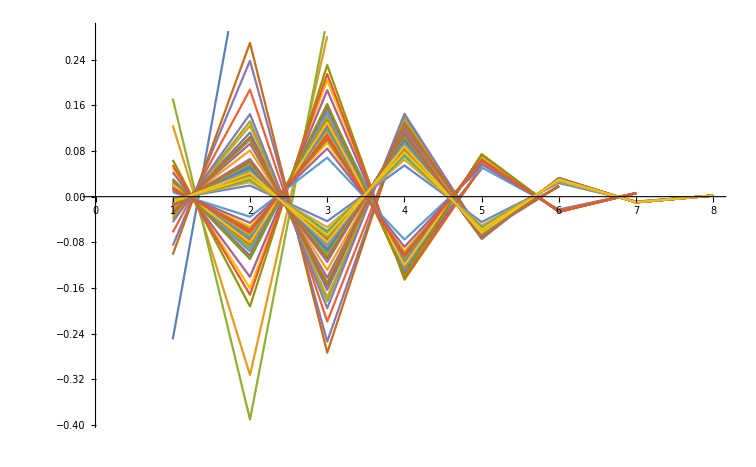

```mathematica
ListLinePlot[Map[
With[
{l=Length[#],all=#},Map[#/(4^l)&,all]]&,{{-4,8},{8,-20,18},{11,-25,20},{-16,48,-56,32},{-22,61,-65,34},{-26,69,-70,35},{32,-112,160,-120,50},{52,-164,209,-140,53},{44,-144,191,-133,52},{66,-197,236,-149,54},{57,-176,220,-145,54},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-114,409,-616,510,-253,76},{-132,460,-669,534,-257,76},{-150,509,-721,562,-265,77},{-162,541,-752,575,-267,77},{-121,429,-636,518,-254,76},{-182,593,-801,595,-270,77},{-120,426,-637,525,-259,77},{128,-576,1120,-1232,840,-364,98},{208,-864,1544,-1560,981,-396,101},{176,-752,1384,-1440,931,-385,100},{228,-932,1641,-1636,1016,-405,102},{264,-1052,1798,-1737,1048,-409,102},{242,-979,1701,-1672,1026,-406,102},{286,-1123,1892,-1805,1078,-417,103},{324,-1244,2045,-1902,1109,-421,103},{300,-1168,1951,-1845,1092,-419,103},{364,-1368,2195,-1991,1135,-424,103},{388,-1440,2285,-2055,1164,-432,104},{404,-1488,2341,-2087,1173,-433,104},{240,-972,1700,-1687,1043,-413,103},{322,-1237,2044,-1917,1126,-428,104},{362,-1361,2194,-2006,1152,-431,104},{430,-1565,2431,-2140,1189,-435,104},{347,-1315,2137,-1969,1139,-429,104},{474,-1693,2574,-2217,1209,-437,104},{502,-1773,2661,-2262,1220,-438,104},{247,-995,1736,-1722,1064,-420,104},{-256,1280,-2816,3584,-2912,1568,-560,128},{-352,1680,-3520,4264,-3302,1701,-585,130},{-456,2092,-4214,4913,-3668,1826,-609,132},{-416,1936,-3952,4664,-3522,1773,-598,131},{-572,2532,-4907,5502,-3961,1912,-623,133},{-724,3084,-5749,6206,-4310,2014,-639,134},{-528,2368,-4648,5272,-3833,1866,-613,132},{-600,2636,-5070,5641,-4029,1930,-625,133},{-648,2812,-5334,5849,-4120,1951,-627,133},{-644,2796,-5325,5878,-4169,1982,-636,134},{-484,2200,-4381,5045,-3724,1838,-610,132},{-480,2184,-4372,5074,-3773,1869,-619,133},{-726,3091,-5750,6191,-4293,2007,-638,134},{-776,3268,-6010,6395,-4383,2028,-640,134},{-860,3560,-6427,6711,-4518,2059,-643,134},{-728,3100,-5758,6177,-4261,1983,-630,133},{-694,2977,-5589,6075,-4247,1997,-637,134},{-944,3844,-6832,7037,-4684,2114,-654,135},{-856,3544,-6418,6740,-4567,2090,-652,135},{-808,3380,-6170,6515,-4433,2039,-641,134},{-1034,4145,-7242,7330,-4800,2138,-656,135},{-948,3860,-6841,7008,-4635,2083,-645,134},{-1000,4032,-7086,7214,-4751,2127,-655,135},{-1092,4336,-7493,7499,-4862,2150,-657,135},{-1004,4048,-7095,7185,-4702,2096,-646,134},{-676,2912,-5489,5991,-4207,1987,-636,134},{-627,2734,-5226,5788,-4120,1967,-634,134}}]]
```

```mathematica
Map[
With[
{l=Length[#],all=#},Map[#/l,all]]&,{{-4,8},{8,-20,18},{11,-25,20},{-16,48,-56,32},{-22,61,-65,34},{-26,69,-70,35},{32,-112,160,-120,50},{52,-164,209,-140,53},{44,-144,191,-133,52},{66,-197,236,-149,54},{57,-176,220,-145,54},{-64,256,-432,400,-220,72},{-88,332,-526,457,-237,74},{-104,380,-582,489,-246,75},{-114,409,-616,510,-253,76},{-132,460,-669,534,-257,76},{-150,509,-721,562,-265,77},{-162,541,-752,575,-267,77},{-121,429,-636,518,-254,76},{-182,593,-801,595,-270,77},{-120,426,-637,525,-259,77},{128,-576,1120,-1232,840,-364,98},{208,-864,1544,-1560,981,-396,101},{176,-752,1384,-1440,931,-385,100},{228,-932,1641,-1636,1016,-405,102},{264,-1052,1798,-1737,1048,-409,102},{242,-979,1701,-1672,1026,-406,102},{286,-1123,1892,-1805,1078,-417,103},{324,-1244,2045,-1902,1109,-421,103},{300,-1168,1951,-1845,1092,-419,103},{364,-1368,2195,-1991,1135,-424,103},{388,-1440,2285,-2055,1164,-432,104},{404,-1488,2341,-2087,1173,-433,104},{240,-972,1700,-1687,1043,-413,103},{322,-1237,2044,-1917,1126,-428,104},{362,-1361,2194,-2006,1152,-431,104},{430,-1565,2431,-2140,1189,-435,104},{347,-1315,2137,-1969,1139,-429,104},{474,-1693,2574,-2217,1209,-437,104},{502,-1773,2661,-2262,1220,-438,104},{247,-995,1736,-1722,1064,-420,104},{-256,1280,-2816,3584,-2912,1568,-560,128},{-352,1680,-3520,4264,-3302,1701,-585,130},{-456,2092,-4214,4913,-3668,1826,-609,132},{-416,1936,-3952,4664,-3522,1773,-598,131},{-572,2532,-4907,5502,-3961,1912,-623,133},{-724,3084,-5749,6206,-4310,2014,-639,134},{-528,2368,-4648,5272,-3833,1866,-613,132},{-600,2636,-5070,5641,-4029,1930,-625,133},{-648,2812,-5334,5849,-4120,1951,-627,133},{-644,2796,-5325,5878,-4169,1982,-636,134},{-484,2200,-4381,5045,-3724,1838,-610,132},{-480,2184,-4372,5074,-3773,1869,-619,133},{-726,3091,-5750,6191,-4293,2007,-638,134},{-776,3268,-6010,6395,-4383,2028,-640,134},{-860,3560,-6427,6711,-4518,2059,-643,134},{-728,3100,-5758,6177,-4261,1983,-630,133},{-694,2977,-5589,6075,-4247,1997,-637,134},{-944,3844,-6832,7037,-4684,2114,-654,135},{-856,3544,-6418,6740,-4567,2090,-652,135},{-808,3380,-6170,6515,-4433,2039,-641,134},{-1034,4145,-7242,7330,-4800,2138,-656,135},{-948,3860,-6841,7008,-4635,2083,-645,134},{-1000,4032,-7086,7214,-4751,2127,-655,135},{-1092,4336,-7493,7499,-4862,2150,-657,135},{-1004,4048,-7095,7185,-4702,2096,-646,134},{-676,2912,-5489,5991,-4207,1987,-636,134},{-627,2734,-5226,5788,-4120,1967,-634,134}}]
```

{{{-2,4}[-4],{-2,4}[8]},{{8/3,-20/3,6}[8],{8/3,-20/3,6}[-20],{8/3,-20/3,6}[18]},65,{{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[-627],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[2734],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[-5226],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[5788],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[-4120],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[1967],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[-634],{-627/8,1367/4,-2613/4,1447/2,-515,1967/8,-317/4,67/4}[134]}}
 |  |  |  |